# Figures 3 and S3: plotting

## Load results

```mathematica
ClearAll["Global`*"];
data=Import[FileNameJoin[{NotebookDirectory[],"Fig3_data.csv"}],"CSV"];
```

## Figure 3

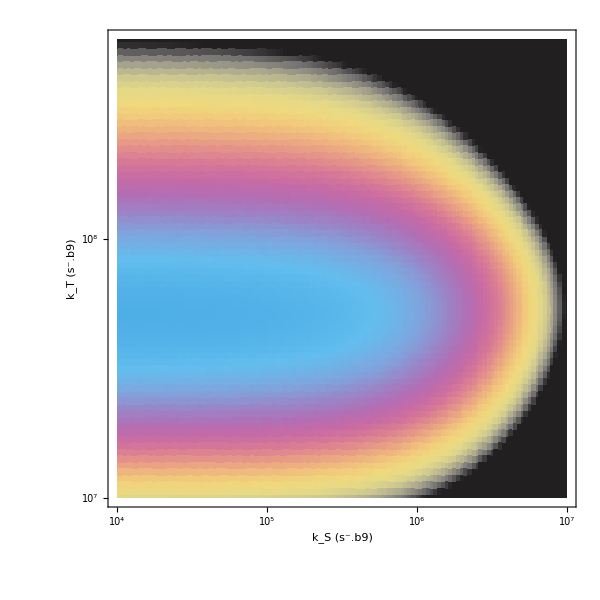

```mathematica
fig3=ListDensityPlot[Transpose[{Log10[data⟦1,2;;All⟧],Log10[data⟦2,2;;All⟧],data⟦4,2;;All⟧}],InterpolationOrder->0,ColorFunction->(ColorData["CMYKColors"][1-#1/0.13]&),ColorFunctionScaling->False,FrameTicksStyle->{14,Thick,Bold},FrameTicks->{{Table[{p,10^p},{p,7,8}],None},{Table[{p,10^p},{p,4,7}],None}},FrameLabel->{"k_S (s⁻.b9)","k_T (s⁻.b9)"},PlotRange->{All,All,{0,0.13}},PlotRangePadding->None,AspectRatio->1,ImageSize->600,PlotLegends->Placed[BarLegend[{(ColorData["CMYKColors"][1-#1/0.13]&),{0,0.13}},LegendLabel->"Logarithmic Negativity",LabelStyle->14,LegendLayout->"Row",LegendMarkerSize->450],Below]];
fig3
```

## Figure S3

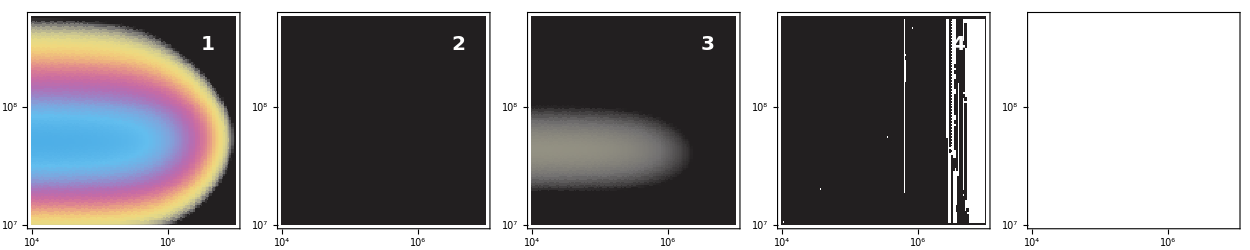
-Graphics-k_S (s⁻.b9)k_T (s⁻.b9)

```mathematica
panels=Table[ListDensityPlot[Transpose[{Log10[data⟦1,2;;All⟧],Log10[data⟦2,2;;All⟧],data⟦m+3,2;;All⟧}],InterpolationOrder->0,ColorFunction->(ColorData["CMYKColors"][1-#1/0.13]&),ColorFunctionScaling->False,FrameTicksStyle->{14,Thick,Bold},FrameTicks->{{Table[{p,10^p},{p,7,8}],None},{Table[{p,10^p},{p,4,7}],None}},PlotRange->{All,All,{0,0.13}},PlotRangePadding->None,AspectRatio->1,ImageSize->250,Epilog->{Inset[Style[ToString[m],White,Bold,20],Scaled[{0.85,0.85}]]}],{m,1,5}];
figS3 = Legended[Labeled[GraphicsRow[panels,Spacings->0.1,ImageSize->1250],{Style["k_S (s⁻.b9)",Bold,14],Rotate[Style["k_T (s⁻.b9)",Bold,14],Pi/2]},{Bottom,Left}],Placed[BarLegend[{(ColorData["CMYKColors"][1-#1/0.13]&),{0,0.13}},LegendLabel->"Logarithmic Negativity",LabelStyle->14,LegendLayout->"Row",LegendMarkerSize->600],Below]];
figS3
```

## Export figures

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Fig3.pdf"}],fig3,"PDF"];
Export[FileNameJoin[{NotebookDirectory[],"Fig3.eps"}],fig3,"EPS"];
Export[FileNameJoin[{NotebookDirectory[],"FigS3.pdf"}],figS3,"PDF"];
Export[FileNameJoin[{NotebookDirectory[],"FigS3.eps"}],figS3,"EPS"];
```